# Eli — PS 13 — 2025-03-25

## EIWL3 Sections 33 and 34

# Chapter 33

```mathematica
(*33.1*)Head[ListPlot[{1, 2}]]
```

Graphics

```mathematica
(*33.2*)Times @@ Range[100]
```

93326215443944152681699238856266700490715968264381621468592963895217599993229915608941463976156518286253697920827223758251185210916864000000000000000000000000

```mathematica
(*33.3*)f @@@ Tuples[{a, b}, 2]
```

{f[a,a],f[a,b],f[b,a],f[b,b]}

```mathematica
(*33.4*)ExpressionTree /@ NestList[#^# &, x, 4]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(*33.5*)Union[Cases[Flatten[Table[i^2/(j^2 + 1), {i, 20}, {j, 20}]],_Integer]]
```

{2,5,8,10,17,18,20,32,40,45,50,72,80,98,128,162,200}

```mathematica
(*33.6*)Graph[Rule @@@ Partition[Table[Mod[n^2 + n, 100], {n, 100}], 2, 1]]
```

-Graphics-

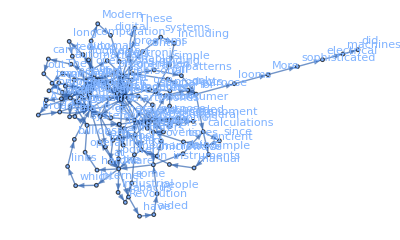

```mathematica
(*33.7*)Graph[Rule @@@ 
  Partition[TextWords[WikipediaData["computers"]][[1 ;; 200]], 2, 1], 
 VertexLabels -> All]
```

```mathematica
(*33.8*)f @@@ Partition[{1, 2, 7, 2, 5, 4} 1, 2]
```

{f[1,2],f[7,2],f[5,4]}

# Chapter 34

```mathematica
(*34.1*)Values[Counts[IntegerDigits[3^100]]]
```

{5,9,5,7,9,7,4,1,1}

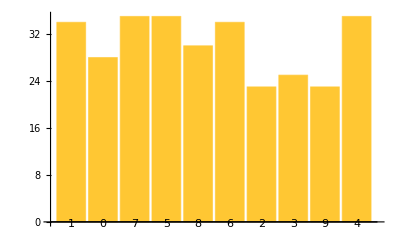

```mathematica
(*34.2*)BarChart[Counts[IntegerDigits[2^1000]],ChartLabels->Automatic]
```

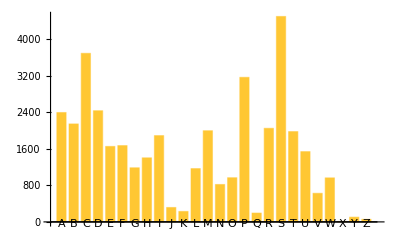

```mathematica
(*34.3*)BarChart[Counts[Capitalize[Characters[WordList[]][[All,1]]]],ChartLabels->Automatic]
```

```mathematica
(*34.4*)Sort[Counts[Capitalize[Characters[WordList[]][[All,1]]]]][[-5;;-1]]
```

<|A→2397,D→2436,P→3168,C→3694,S→4502|>

```mathematica
(*34.5*)N[LetterCounts[WikipediaData[]][]/LetterCounts[WikipediaData[]][]]
```

WikipediaData::invinp0: Invalid input.

LetterCounts::arg1: String or list of strings expected in position 1.

WikipediaData::invinp0: Invalid input.

LetterCounts::arg1: String or list of strings expected in position 1.

1.

```mathematica
(*34.6*)Keys[Sort[Counts[TextWords[ExampleData[{, }]]]][[-10;;-1]]]
```

ExampleData::notcoll: Null is not a known collection for ExampleData. Use ExampleData[] for a list of collections.

TextWords::arg1: String or ContentObject expected at position 1.

Counts::invrp: The argument TextWords[ExampleData[{Null,Null}]] is not a valid Association or a list.

Part::take: Cannot take positions -10 through -1 in Counts[TextWords[ExampleData[{Null,Null}]]].

Keys::invrl: The argument Counts[TextWords[ExampleData[{Null,Null}]]]⟦-10;;-1⟧ is not a valid Association or a list of rules.

Keys[Counts[TextWords[ExampleData[{Null,Null}]]]⟦-10;;-1⟧]